```mathematica
CfgDecorrelationTime[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"rods"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
tcorrs=Table[{(j-t)*dt,
Cos[anglesT[[j,i]]-anglesT[[t,i]]]},
{t,1,Length[rt],100},(*Length[rt]},*)
{j,t,Length[rt]},
{i,Length[rt[[t]]]}];
gatheredCorrs = Gather[Flatten[tcorrs,2],First[#1]==First[#2]&];
decor=Table[Mean[gc],{gc,gatheredCorrs}];
decor
];
```

```mathematica
mdwout = "/Volumes/homes/Code/cytomod/shila/semiflexible/out/network/";
mdwlcl="/home/simonfreedman/scratch-midway/cytomod/out/pl/";
mdwhm="/home/simonfreedman/Code/cytomod/shila/semiflexible/out/pl/";
ParticleTimeSeries[d_,n_]:=
Module[
{dir=d, name=n},
file=dir<>"/txt_stack/"<>name<>".txt";
particles=Import[file,"Table"];
Print["Finished importing "<>file];
timestamps = Position[particles,"t"][[All,1]];
particlesT=Table[particles[[timestamps[[i]]+1;;timestamps[[i+1]]-1]],{i,Length[timestamps]-1}];
particlesT=Append[particlesT, particles[[timestamps[[-1]]+1;;]]];
nparticles=Length[particlesT[[1]]];
dt=particles[[timestamps[[2]],3]]-particles[[timestamps[[1]],3]];
{nparticles, dt,particlesT}
];
DecorrelationTime[d_]:=
Module[
{dir =d},
{np, dt,rt}=ParticleTimeSeries[d,"links"];
anglesT=ArcTan[rt[[All,All,3]],rt[[All,All,4]]];
anglesBwT = Differences[anglesT,{0,1}];
tcorrs=Table[{(j-t)*dt,
anglesBwT[[j,i]]*anglesBwT[[t,i]]},
{t,Ceiling[Length[anglesBwT]/2],Length[anglesBwT],100},
{j,t,Min[t+1000,Length[anglesBwT]],5},
{i,Length[anglesBwT[[t]]]}];
gatheredCorrs = Gather[Flatten[tcorrs,2],First[#1]==First[#2]&];
decor=Table[Mean[gc],{gc,gatheredCorrs}];
decor
];
```

```mathematica
seeds=Table[ToString[i],{i,4421,4440}];
basedir="nm200_bwd_bend_seed";
dirs=Table[mdwlcl<>basedir<>s,{s,seeds}];
```

```mathematica
dirs[[1]]
```

/home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_bwd_bend_seed4421

```mathematica
ts=DecorrelationTime[dirs[[1]]];
```

Finished importing /home/simonfreedman/scratch-midway/cytomod/out/pl/nm200_bwd_bend_seed4421/txt_stack/links.txt

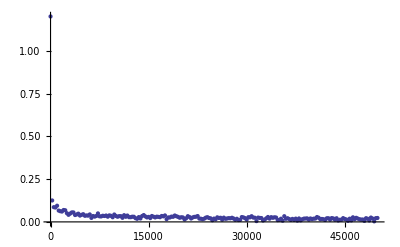

```mathematica
ListPlot[ts,PlotRange->Full]
```